```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
```

## Preparation

```mathematica
eqs=<<eqs.m;
bcsz0=<<bcsz0.m;
bcsz1=<<bcsz1.m;
jacobi=<<jacobi.m;
jacobiz0=<<jacobiz0.m;
jacobiz1=<<jacobiz1.m;
monitor=<<monitor.m;
(*Parameters*)
L=1;Lz=1.0;Lx=N[2π];
A0=1.5;k0=2;
mu=1.4;t=0.043;T=t mu;
zh=1/6 (4 π T+√(16 π^2 T^2+6 mu^2));
Nz=30;Nx=60;Nzx=Nz*Nx;
Eye=IdentityMatrix[Nzx];Zero=ConstantArray[0,{Nzx,Nzx}];
(*Chebshev谱求导矩阵生成函数*)
chebp[n_]:=Table[Cos[(i π)/(n-1.0)],{i,0,n-1}];
cheb[n_,l_]:=Module[{x,c,sdm},x=chebp[n];c=Table[If[i==1||i==n,2.0,1.0],{i,1,n}];sdm=2/l Table[If[i≠j,c[[i]]/c[[j]](-1)^(i+j)/(x[[i]]-x[[j]]),0],{i,1,n},{j,1,n}];sdm-=DiagonalMatrix[Total[sdm,{2}]]];
dz=cheb[Nz,Lz];
dzs[0]=IdentityMatrix[Nz];dzs[1]=dz;dzs[2]=dz.dz;
gridz=0.5(chebp[Nz]+1);zz=gridz⊗ConstantArray[1,Nx];Z=Flatten[zz];
(*boundary index of holographic coordinate*)
z1=Flatten[Position[Z,n_/;n==gridz⟦1⟧]];z0=Flatten[Position[Z,n_/;n==gridz⟦-1⟧]];
zb=Join[z0,z1];
(*Fourier谱求导矩阵生成函数*)
fourier[n_,l_]:=π/l Table[If[i==j,0,(-1)^(i-j)If[Mod[n,2]==0,Cot[(π*(i-j))/n],Csc[(π*(i-j))/n]]],{i,1,n},{j,1,n}];
dx=fourier[Nx,Lx];
dxs[0]=IdentityMatrix[Nx];dxs[1]=dx;dxs[2]=dx.dx;
gridx=Lx/Nx Range[0,Nx-1];xx=ConstantArray[1,Nz]⊗gridx;X=Flatten[xx];
(*derivative matrix after vectorization*)
Do[If[i+j≤ 2,ds[i,j]=KroneckerProduct[dzs[i],dxs[j]]],{i,0,2},{j,0,2}];
```

## Solution

### initialization

```mathematica
q[1]=s[Q1]=ConstantArray[1,Nzx];
q[2]=s[Q2]=ConstantArray[1,Nzx];
q[3]=s[Q3]=ConstantArray[0,Nzx];
q[4]=s[Q4]=ConstantArray[1,Nzx];
q[5]=s[Q5]=ConstantArray[1,Nzx];
(*q[6]=s[Q6]=<<Q6probelimit.m;
q[7]=s[Q7]=<<Q7probelimit.m;*)
q[6]=s[Q6]=0.1Cos[k0 X];
q[7]=s[Q7]=ConstantArray[mu,Nzx];
(*q[1]=s[Q1]=<<Q1.m;
q[2]=s[Q2]=<<Q2.m;
q[3]=s[Q3]=<<Q3.m;
q[4]=s[Q4]=<<Q4.m;
q[5]=s[Q5]=<<Q5.m;
q[6]=s[Q6]=<<Q6.m;
q[7]=s[Q7]=<<Q7.m;*)
(*j=5;
q[1]=s[Q1]=ReadList["Q1.m"]⟦j⟧;
q[2]=s[Q2]=ReadList["Q2.m"]⟦j⟧;
q[3]=s[Q3]=ReadList["Q3.m"]⟦j⟧;
q[4]=s[Q4]=ReadList["Q4.m"]⟦j⟧;
q[5]=s[Q5]=ReadList["Q5.m"]⟦j⟧;
q[6]=s[Q6]=ReadList["Q6.m"]⟦j⟧;
q[7]=s[Q7]=ReadList["Q7.m"]⟦j⟧;*)
(*reshape*)
(*Do[req[i]=ArrayReshape[q[i],{Nz,Nx}],{i,7}];
(*interpolate function*)
Do[interfunq[i]=ListInterpolation[Append[req[i]ᵀ,req[i]⟦;;,1⟧]ᵀ,{gridz,Append[gridx,0.5Lx]}],{i,7}];*)
```

### interpolation(非必要)

```mathematica
(*resample*)
Do[q[k]=Flatten[Table[interfunq[k][gridz⟦i⟧,gridx⟦j⟧],{i,Nz},{j,Nx}]],{k,7}];
{s[Q1],s[Q2],s[Q3],s[Q4],s[Q5],s[Q6],s[Q7]}={q[1],q[2],q[3],q[4],q[5],q[6],q[7]};
```

### iteration

```mathematica
seed=Join[q[1],q[2],q[3],q[4],q[5],q[6],q[7]];length=Length[seed];
eps=10^-10;k=0;kmax=12;done=1;rmssollist={};
Monitor[While[done==1&&k<kmax,
diseqs=eqs/.{Derivative[i_,j_][h_][z,x]->ds[i,j].s[h],h_[z,x]->s[h],z->Z};
disbcsz0=bcsz0/.{Derivative[i_,j_][h_][z,x]:>(ds[i,j]⟦z0⟧).s[h],h_[z,x]:>s[h]⟦z0⟧,x:>X⟦z0⟧};
disbcsz1=bcsz1/.{Derivative[i_,j_][h_][z,x]:>(ds[i,j]⟦z1⟧).s[h],h_[z,x]:>s[h]⟦z1⟧};
diseqs⟦;;,z0⟧=disbcsz0;
diseqs⟦;;,z1⟧=disbcsz1;
b=-Flatten[diseqs];
J=jacobi/.{Derivative[i_,j_][h_][z,x]->ds[i,j].s[h],h_[z,x]->s[h],Subscript[d, i_,j_]->ds[i,j],eye->Eye,zero->Zero,z->Z};
Jz0=jacobiz0/.{Derivative[i_,j_][h_][z,x]:> (ds[i,j]⟦z0⟧).s[h],h_[z,x]:> s[h]⟦z0⟧,Subscript[d, i_,j_]:> ds[i,j]⟦z0⟧,eye:> Eye⟦z0⟧,zero:> Zero⟦z0⟧};
Jz1=jacobiz1/.{Derivative[i_,j_][h_][z,x]:> (ds[i,j]⟦z1⟧).s[h],h_[z,x]:> s[h]⟦z1⟧,Subscript[d, i_,j_]:> ds[i,j]⟦z1⟧,eye:> Eye⟦z1⟧,zero:> Zero⟦z1⟧};
J⟦;;,;;,z0⟧=Jz0;
J⟦;;,;;,z1⟧=Jz1;
J=ArrayFlatten[J];
sol=LinearSolve[J,b];(*bottleneck*)
seed+=sol;k++;
reseed=ArrayReshape[seed,{7,Nzx}];
q[1]=s[Q1]=reseed⟦1⟧;
q[2]=s[Q2]=reseed⟦2⟧;
q[3]=s[Q3]=reseed⟦3⟧;
q[4]=s[Q4]=reseed⟦4⟧;
q[5]=s[Q5]=reseed⟦5⟧;
q[6]=s[Q6]=reseed⟦6⟧;
q[7]=s[Q7]=reseed⟦7⟧;
rmssol=√(Total[sol^2]/length);
AppendTo[rmssollist,rmssol];
If[rmssol≤eps,done=0;Print[rmssollist]];
],rmssollist];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{0.188204,0.019606,0.00103083,0.0000169129,2.37476×10^-9,1.20195×10^-13}

### visualization

-Graphics3D-

-Graphics3D-

-Graphics3D-

«4 more identical outputs»

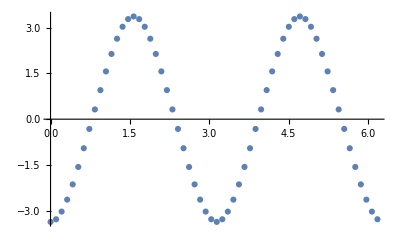

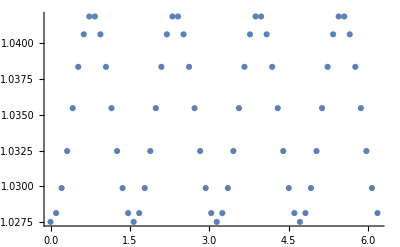

```mathematica
Do[solq[i]=ArrayReshape[q[i],{Nz,Nx}],{i,7}];
orderp=zh(dz⟦-1⟧.solq[6]);
density=zh(mu-(dz⟦-1⟧.solq[7]));
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq[6]⟦i,j⟧},{i,Nz},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq[7]⟦i,j⟧},{i,Nz},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq[1]⟦i,j⟧},{i,Nz},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq[2]⟦i,j⟧},{i,Nz},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq[3]⟦i,j⟧},{i,Nz},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq[4]⟦i,j⟧},{i,Nz},{j,Nx}],1],PlotRange->All]
ListPlot3D[Flatten[Table[{gridz⟦i⟧,gridx⟦j⟧,solq[5]⟦i,j⟧},{i,Nz},{j,Nx}],1],PlotRange->All]
ListPlot[Table[{gridx⟦i⟧,orderp⟦i⟧},{i,1,Nx}],PlotRange->All]
ListPlot[Table[{gridx⟦i⟧,density⟦i⟧},{i,1,Nx}],PlotRange->All]
```

### check DeTurck vector

```mathematica
submonitor=monitor/.{Derivative[i_,j_][h_][z,x]->ds[i,j].s[h],h_[z,x]->s[h],z->Z};
submonitor⟦zb⟧=0;
normxi=Norm[submonitor]
```

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

General::stop: 在本次计算中，Infinity::indet 的进一步输出将被抑制.

1.29128×10^-9